```mathematica
Subscript[f, 1]=(Subscript[x, 0]-Subscript[x, 1])/(Subscript[a, 1] Subscript[x, 0]+ Subscript[b, 1] Subscript[x, 1] + Subscript[c, 1]);
Subscript[f, 2]=(Subscript[x, 1]-Subscript[x, 2])/(Subscript[a, 2] Subscript[x, 1]+ Subscript[b, 2] Subscript[x, 2] + Subscript[c, 2]);
Subscript[f, 3]=(Subscript[x, 2])/(Subscript[a, 3] Subscript[x, 2]+ Subscript[c, 3]);
Obj=1/Subscript[f, 1]+1/Subscript[f, 2]+1/Subscript[f, 3];
ObjEqs={D[Obj,Subscript[x, 1]]==0,D[Obj,Subscript[x, 2]]==0};
Subscript[Solxi, 1]=Solve[ObjEqs[[2]],Subscript[x, 1]];
Subscript[ξ, 1]=Subscript[x, 1]/.(Subscript[Solxi, 1][[2]]);
Subscript[Solxi, 0]=Solve[ObjEqs[[1]],Subscript[x, 0]];
Subscript[ξ, 0]=Subscript[x, 0]/.(Subscript[Solxi, 0][[1]])/.{Subscript[x, 1]->Subscript[ξ, 1]};
samepars={Subscript[c, 3]->Subscript[a, 3]+Subscript[b, 3],Subscript[c, 2]->Subscript[a, 2]+Subscript[b, 2],Subscript[c, 1]->Subscript[a, 1]+Subscript[b, 1]}
samepars={Subscript[c, 3]->Subscript[c, 2],Subscript[b, 2]->Subscript[a, 1]+Subscript[b, 1]-Subscript[a, 2]}
assumptions={Subscript[x, 2]>0,Subscript[a, 1]>0,Subscript[a, 2]>0,Subscript[a, 3]>0,Subscript[b, 1]>0,Subscript[b, 2]>0,Subscript[c, 1]>0,Subscript[c, 2]>0};
Subscript[ξ, 1]=Simplify[Subscript[ξ, 1]/.samepars,Assumptions->assumptions]
Subscript[ξ, 0]=Simplify[Subscript[ξ, 0]/.samepars,Assumptions->assumptions]
Subscript[g, 1]=Simplify[1/Subscript[f, 1]/.{Subscript[x, 0]->Subscript[ξ, 0],Subscript[x, 1]->Subscript[ξ, 1]},Assumptions->assumptions];
Subscript[g, 2]=Simplify[1/Subscript[f, 2]/.{Subscript[x, 0]->Subscript[ξ, 0],Subscript[x, 1]->Subscript[ξ, 1]},Assumptions->assumptions];
Subscript[g, 3]=Simplify[1/Subscript[f, 3]/.{Subscript[x, 0]->Subscript[ξ, 0],Subscript[x, 1]->Subscript[ξ, 1]},Assumptions->assumptions];
Subscript[ϵ, 1]=Subscript[g, 1]/(Subscript[g, 1]+Subscript[g, 2]+Subscript[g, 3])//Simplify;
Subscript[ϵ, 2]=Subscript[g, 2]/(Subscript[g, 1]+Subscript[g, 2]+Subscript[g, 3])//Simplify;
Subscript[ϵ, 3]=Subscript[g, 3]/(Subscript[g, 1]+Subscript[g, 2]+Subscript[g, 3])//Simplify
```

{c_3→a_3+b_3,c_2→a_2+b_2,c_1→a_1+b_1}

{c_3→c_2,b_2→a_1-a_2+b_1}

x_2 (2+((a_1+b_1) x_2)/c_2)

(x_2 (4 c_2^2+3 (a_1+b_1) c_2 x_2+a_1^2 x_2^2+2 a_1 b_1 x_2^2+b_1^2 x_2^2+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+(a_1+b_1) x_2 (8 c_2^2+5 (a_1+b_1) c_2 x_2+(a_1+b_1)^2 x_2^2)))))/(2 c_2^2)

(a_3+c_3/x_2)/(a_3+c_3/x_2+(c_2^2+(2 a_2+b_2) c_2 x_2+a_2 (a_1+b_1) x_2^2)/(x_2 (c_2+(a_1+b_1) x_2))+(2 c_1 c_2^2+x_2 (a_1^3 x_2^2+2 b_1 c_2 (2 c_2+b_1 x_2)+a_1^2 x_2 (3 c_2+2 b_1 x_2)+a_1 (4 c_2^2+5 b_1 c_2 x_2+b_1^2 x_2^2+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+(a_1+b_1) x_2 (8 c_2^2+5 (a_1+b_1) c_2 x_2+(a_1+b_1)^2 x_2^2))))))/(x_2 (b_1 c_2 x_2+a_1^2 x_2^2+b_1^2 x_2^2+a_1 x_2 (c_2+2 b_1 x_2)+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+(a_1+b_1) x_2 (8 c_2^2+5 (a_1+b_1) c_2 x_2+(a_1+b_1)^2 x_2^2))))))

```mathematica
QststEqs={Subscript[e, 1] Subscript[f, 1]==Subscript[e, 2] Subscript[f, 2],Subscript[e, 3] Subscript[f, 3]==Subscript[e, 2] Subscript[f, 2]}
```

{(e_1 (x_0-x_1))/(c_1+a_1 x_0+b_1 x_1)==(e_2 (x_1-x_2))/(c_2+a_2 x_1+b_2 x_2),(e_3 x_2)/(c_3+a_3 x_2)==(e_2 (x_1-x_2))/(c_2+a_2 x_1+b_2 x_2)}

```mathematica
x2stst=Solve[QststEqs[[2]],{Subscript[x, 2]}]
```

{{x_2→(-c_3 e_2-c_2 e_3+a_3 e_2 x_1-a_2 e_3 x_1-√(4 c_3 e_2 (a_3 e_2+b_2 e_3) x_1+(c_3 e_2+c_2 e_3-a_3 e_2 x_1+a_2 e_3 x_1)^2))/(2 (a_3 e_2+b_2 e_3))},{x_2→(-c_3 e_2-c_2 e_3+a_3 e_2 x_1-a_2 e_3 x_1+√(4 c_3 e_2 (a_3 e_2+b_2 e_3) x_1+(c_3 e_2+c_2 e_3-a_3 e_2 x_1+a_2 e_3 x_1)^2))/(2 (a_3 e_2+b_2 e_3))}}

```mathematica
x1sols=Solve[QststEqs[[1]]/.x2stst[[2]],{Subscript[x, 1]}];
x1stst=x1sols[[2]]
```

$Aborted

{x_1→-(a_3 c_2 e_1^2-b_2 c_3 e_1^2+a_3 c_1 e_1 e_2+b_1 c_3 e_1 e_2+a_2 c_1 e_1 e_3+b_1 c_2 e_1 e_3+2 b_1 c_1 e_2 e_3-2 a_2 a_3 e_1^2 x_0+a_1 a_3 e_1 e_2 x_0-a_3 b_1 e_1 e_2 x_0+a_1 a_2 e_1 e_3 x_0-a_2 b_1 e_1 e_3 x_0+2 a_1 b_1 e_2 e_3 x_0)/(3 (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))+((1+ⅈ √3) (-(16+2 a_1 b_1 e_2 e_3 x_0)^2+3 (1) (c_1 c_3 e_1 e_2+c_1 c_2 e_1 e_3+20+a_1^2 e_2 e_3 x_0^2)))/(3 2^(2/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3) (-2 a_3^3 c_2^3 e_1^6+510+√(1^2+4 1))^(1/3))-((1-ⅈ √3) ((-2 a_3^3 c_2^3 e_1^6+510+√((1)^2+4 ((11)^3)))^(1/3))/(6 2^(1/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))}
 |  |  |  |

x_1→-(a_3 c_2 e_1^2-b_2 c_3 e_1^2+a_3 c_1 e_1 e_2+b_1 c_3 e_1 e_2+a_2 c_1 e_1 e_3+b_1 c_2 e_1 e_3+2 b_1 c_1 e_2 e_3-2 a_2 a_3 e_1^2 x_0+a_1 a_3 e_1 e_2 x_0-a_3 b_1 e_1 e_2 x_0+a_1 a_2 e_1 e_3 x_0-a_2 b_1 e_1 e_3 x_0+2 a_1 b_1 e_2 e_3 x_0)/(3 (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))+((1+ⅈ √3) (-(16+2 a_1 b_1 e_2 e_3 x_0)^2+3 (1) (c_1 c_3 e_1 e_2+c_1 c_2 e_1 e_3+20+a_1^2 e_2 e_3 x_0^2)))/(3 2^(2/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3) (-2 a_3^3 c_2^3 e_1^6+510+√(1^2+4 1))^(1/3))-((1-ⅈ √3) ((-2 a_3^3 c_2^3 e_1^6+510+√((1)^2+4 ((11)^3)))^(1/3))/(6 2^(1/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))
 |  |  |  |

```mathematica
x1stst=x1sols[[1]]
```

{x_1→-(a_3 c_2 e_1^2-b_2 c_3 e_1^2+a_3 c_1 e_1 e_2+b_1 c_3 e_1 e_2+a_2 c_1 e_1 e_3+b_1 c_2 e_1 e_3+2 b_1 c_1 e_2 e_3-2 a_2 a_3 e_1^2 x_0+a_1 a_3 e_1 e_2 x_0-a_3 b_1 e_1 e_2 x_0+a_1 a_2 e_1 e_3 x_0-a_2 b_1 e_1 e_3 x_0+2 a_1 b_1 e_2 e_3 x_0)/(3 (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))-(2^(1/3) (-(16+2 a_1 b_1 e_2 e_3 x_0)^2+3 (a_2 a_3 e_1^2+2+1) (c_1 c_3 e_1 e_2+c_1 c_2 e_1 e_3+20+a_1^2 e_2 e_3 x_0^2)))/(3 (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3) (-2 a_3^3 c_2^3 e_1^6+510+√(1^2+4 1))^(1/3))+((-2 a_3^3 c_2^3 e_1^6+509+2 4 x_0^3+√((1)^2+4 (1)^3))^(1/3))/(3 2^(1/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))}
 |  |  |  |

```mathematica
Subscript[h, 1]=1/Subscript[f, 1]/.{Subscript[x, 1]->Subscript[ξ, 1]};
Subscript[h, 2]=1/Subscript[f, 2]/.{Subscript[x, 1]->Subscript[ξ, 1]};
Subscript[h, 3]=1/Subscript[f, 3]/.{Subscript[x, 1]->Subscript[ξ, 1]};
Subscript[η, 1]=Subscript[h, 1]/(Subscript[h, 1]+Subscript[h, 2]+Subscript[h, 3]);
FluxEta=FullSimplify[Subscript[η, 1] Subscript[f, 1]/.{Subscript[x, 1]->Subscript[ξ, 1]},Assumptions->{assumptions,(2 Subscript[c, 2]+(Subscript[a, 1]+Subscript[b, 1]) Subscript[x, 2])>0}]
```

1/(a_2+a_3-b_1+(c_2+c_3)/x_2+((-a_1+a_2-b_1+b_2) c_2)/(c_2+(a_1+b_1) x_2)+(c_2 (c_1+(a_1+b_1) x_0))/(c_2 (x_0-2 x_2)-(a_1+b_1) x_2^2))

```mathematica
FluxE=Subscript[e, 1] Subscript[f, 1]/.x1stst
FluxEps=Subscript[ϵ, 1] Subscript[f, 1]/.x1stst/.{Subscript[e, 1]->Subscript[ϵ, 1],Subscript[e, 2]->Subscript[ϵ, 2],Subscript[e, 3]->Subscript[ϵ, 3]}
```

(e_1 (x_0+(16+2 a_1 b_1 e_2 e_3 x_0)/(3 (1))+(2^1 1)/1-((-2 a_3^3 c_2^3 e_1^6+510+√1)^(1/3))/(3 2^(1/3) (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))))/(c_1+a_1 x_0+b_1 (-(a_3 c_2 e_1^2-b_2 c_3 e_1^2+a_3 c_1 e_1 e_2+12+2 a_1 b_1 e_2 e_3 x_0)/(3 (a_2 a_3 e_1^2+a_3 b_1 e_1 e_2+a_2 b_1 e_1 e_3+b_1^2 e_2 e_3))-111/1+(1)^(1/3)/(3 2^111 (1))))
 |  |  |  |

(2 (c_2+(a_1+b_1) x_2) (2 c_1 c_2^2+1+a_1 x_2 √1) (x_0+((8 4 (c_2^2+1+a_2 (a_1+b_1) x_2^2))/(1)^2+16)/(3 ((4 4)/(1)^2+1/1+1+(4 3 1^2)/(1^2 1^2)))+1-((((128 b_1^3 c_1^3 (1)^3 (c_2+1)^3 (c_2^2+1+a_2 (a_1+b_1) x_2^2)^3)/((2 c_2^2+2+√((c_2+1) 1))^6)+(384 7)/(((11)^6)+510+√((1)^2+4 (1)^3)))^(1/3))/(3 2^1 ((4 b_1^2 (c_3+a_3 x_2) (c_2+(a_1+b_1) x_2) (c_2^2+(2 a_2+b_2) c_2 x_2+a_2 (a_1+b_1) x_2^2))/((2 c_2^2+(a_1+b_1) x_2 (1)+1+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+(a_1+b_1) x_2 (1))))^2)+(4 4 (2 c_1 c_2^2+1+a_1 x_2 √1))/(((a_1+b_1) c_2 x_2+1+√1) 1^2)+1/1+(4 a_2 a_3 (c_2+1)^2 (2 c_1 c_2^2+1+a_1 x_2 √((1) 1))^2)/(((a_1+b_1) c_2 x_2+1+√((c_2+1) 1))^2 (1)^2)))))/(((a_1+b_1) c_2 x_2+(a_1+b_1)^2 x_2^2+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+(a_1+b_1) x_2 (8 c_2^2+5 (a_1+b_1) c_2 x_2+(a_1+b_1)^2 x_2^2)))) (2 c_2^2+(a_1+b_1) x_2 (2 c_3+(a_1+2 1-b_1) 1)+c_2 1+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+1))) (c_1+a_1 x_0+b_1 (-((8 b_1 c_1 (c_3+a_3 x_2) (c_2+(a_1+b_1) x_2) (c_2^2+(2 a_2+b_2) c_2 x_2+a_2 (a_1+b_1) x_2^2))/((2 c_2^2+(a_1+b_1) x_2 (1)+1+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+1)))^2)+(8 5 (c_2^2+1+1))/(1)^2+15)/(3 ((4 b_1^2 (c_3+a_3 x_2) (c_2+(a_1+b_1) x_2) (c_2^2+(2 a_2+b_2) c_2 x_2+a_2 (a_1+b_1) x_2^2))/((2 c_2^2+(a_1+b_1) x_2 (1)+1+√((c_2+(a_1+b_1) x_2) (4 c_1 c_2^2+1)))^2)+(4 4 (2 c_1 c_2^2+1+1))/((1+1+√1) 1)+1+(4 a_2 a_3 (c_2+1)^2 (2 c_1 c_2^2+1+a_1 x_2 √1)^2)/(((a_1+b_1) c_2 x_2+1+√1)^2 (1)^2)))-(2^(1/3) (-(1)^2+3 (1) (1)))/(3 (1) (1)^(1/3))+(1)^(1/3)/1)))
 |  |  |  |

{a_1→1,b_1→2,c_1→1,a_2→2,b_2→3,c_2→1,a_3→3,c_3→2,x_0→10}

{a_1→1,b_1→1,c_1→1,a_2→1,b_2→1,c_2→1,a_3→1,c_3→1,x_0→10}

0.333333

1/(1+2/x_2+21/(10-2 x_2-2 x_2^2))

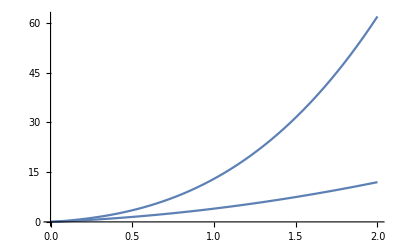

-Graphics-

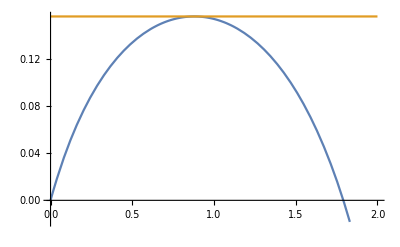

```mathematica
pars={Subscript[a, 1]->1,Subscript[b, 1]->2,Subscript[c, 1]->1,Subscript[a, 2]->2,Subscript[b, 2]->3,Subscript[c, 2]->1,Subscript[a, 3]->3,Subscript[c, 3]->2,Subscript[x, 0]->10}
pars2={Subscript[a, 1]->1,Subscript[b, 1]->1,Subscript[c, 1]->1,Subscript[a, 2]->1,Subscript[b, 2]->1,Subscript[c, 2]->1,Subscript[a, 3]->1,Subscript[c, 3]->1,Subscript[x, 0]->10}
Subscript[ϵ, 1]/.pars2/.{Subscript[x, 2]->1}//N
FluxEta/.pars2
Plot[{Subscript[ξ, 0],Subscript[ξ, 1]}/.pars2,{Subscript[x, 2],0,2}]
Plot[{Subscript[ϵ, 1],Subscript[ϵ, 2],Subscript[ϵ, 3]}/.pars2,{Subscript[x, 2],0,2}]
Plot[{FluxEta/.pars2,fluxpars},{Subscript[x, 2],0,2}]
```

```mathematica
difference=FluxEps-FluxEta;
Simplify[difference/.pars]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

$Aborted

```mathematica
ClearAll["Global`*"]
P=Subscript[c, 1]/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 2]/(Subscript[x, 2]-Subscript[A, 2]) (Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 3]/(Subscript[x, 3]-Subscript[A, 3])(Subscript[x, 2]+Subscript[B, 2])/(Subscript[x, 2]-Subscript[A, 2])(Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1])
```

c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))+(c_3 (B_1+x_1) (B_2+x_2))/((-A_1+x_1) (-A_2+x_2) (-A_3+x_3))

```mathematica
Y={Subscript[x, 1]->Subscript[y, 1],Subscript[x, 2]->Subscript[y, 2],Subscript[x, 3]->Subscript[y, 3]}
X={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}
η = {Subscript[x, 1]->Subscript[A, 1] + (Subscript[y, 2]+Subscript[B, 2])(Subscript[y, 2]-Subscript[A, 2])/(Subscript[A, 2]+Subscript[B, 2]),Subscript[x, 2]->Subscript[y, 2],Subscript[x, 3]->Subscript[y, 3]}
λ = Total[X/.Y]/Total[X/.η]
LY={Subscript[x, 1]->λ(Subscript[A, 1] + (Subscript[y, 2]+Subscript[B, 2])(Subscript[y, 2]-Subscript[A, 2])/(Subscript[A, 2]+Subscript[B, 2])),Subscript[x, 2]->λ Subscript[y, 2],Subscript[x, 3]->λ Subscript[y, 3]}
PLY=P/.LY
PLY-P/.Y
```

{x_1→y_1,x_2→y_2,x_3→y_3}

{x_1,x_2,x_3}

{x_1→A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2),x_2→y_2,x_3→y_3}

(y_1+y_2+y_3)/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)

{x_1→((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3),x_2→(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3),x_3→(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)}

c_1/(-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3))+(c_2 (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))+(c_3 (B_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_3+(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))

-c_1/(-A_1+y_1)-(c_2 (B_1+y_1))/((-A_1+y_1) (-A_2+y_2))-(c_3 (B_1+y_1) (B_2+y_2))/((-A_1+y_1) (-A_2+y_2) (-A_3+y_3))+c_1/(-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3))+(c_2 (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))+(c_3 (B_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_3+(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))

```mathematica
difference = -Subscript[c, 1]/(-Subscript[A, 1]+Subscript[y, 1])-(Subscript[c, 2] (Subscript[B, 1]+Subscript[y, 1]))/((-Subscript[A, 1]+Subscript[y, 1]) (-Subscript[A, 2]+Subscript[y, 2]))-(Subscript[c, 3] (Subscript[B, 1]+Subscript[y, 1]) (Subscript[B, 2]+Subscript[y, 2]))/((-Subscript[A, 1]+Subscript[y, 1]) (-Subscript[A, 2]+Subscript[y, 2]) (-Subscript[A, 3]+Subscript[y, 3]))+Subscript[c, 1]/(-Subscript[A, 1]+((Subscript[A, 1]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])) (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3]))+(Subscript[c, 2] (Subscript[B, 1]+((Subscript[A, 1]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])) (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])))/((-Subscript[A, 2]+(Subscript[y, 2] (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])) (-Subscript[A, 1]+((Subscript[A, 1]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])) (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])))+(Subscript[c, 3] (Subscript[B, 2]+(Subscript[y, 2] (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])) (Subscript[B, 1]+((Subscript[A, 1]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])) (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])))/((-Subscript[A, 2]+(Subscript[y, 2] (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])) (-Subscript[A, 1]+((Subscript[A, 1]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])) (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])) (-Subscript[A, 3]+(Subscript[y, 3] (Subscript[y, 1]+Subscript[y, 2]+Subscript[y, 3]))/(Subscript[A, 1]+Subscript[y, 2]+((-Subscript[A, 2]+Subscript[y, 2]) (Subscript[B, 2]+Subscript[y, 2]))/(Subscript[A, 2]+Subscript[B, 2])+Subscript[y, 3])))
```

-c_1/(-A_1+y_1)-(c_2 (B_1+y_1))/((-A_1+y_1) (-A_2+y_2))-(c_3 (B_1+y_1) (B_2+y_2))/((-A_1+y_1) (-A_2+y_2) (-A_3+y_3))+c_1/(-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3))+(c_2 (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))+(c_3 (B_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_3+(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))

```mathematica
diffspecial=difference/.{Subscript[c, 1]->Subscript[A, 1]+Subscript[B, 1],Subscript[c, 2]->Subscript[A, 2]+Subscript[B, 2],Subscript[c, 3]->Subscript[A, 3]+Subscript[B, 3]}
Simplify[diffspecial,Assumptions->{Subscript[y, 1]> Subscript[A, 1],Subscript[y, 2]>Subscript[A, 2],Subscript[y, 3]>Subscript[A, 3]}]
```

-(A_1+B_1)/(-A_1+y_1)-((A_2+B_2) (B_1+y_1))/((-A_1+y_1) (-A_2+y_2))-((A_3+B_3) (B_1+y_1) (B_2+y_2))/((-A_1+y_1) (-A_2+y_2) (-A_3+y_3))+(A_1+B_1)/(-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3))+((A_2+B_2) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))+((A_3+B_3) (B_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_3+(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))

(A_1+B_1)/(A_1-y_1)-((A_2+B_2) (B_1+y_1))/((A_1-y_1) (A_2-y_2))+((A_3+B_3) (B_1+y_1) (B_2+y_2))/((A_1-y_1) (A_2-y_2) (A_3-y_3))+(A_1+B_1)/(-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3))+((A_2+B_2) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))+((A_3+B_3) (B_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (B_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))/((-A_2+(y_2 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_1+((A_1+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)) (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)) (-A_3+(y_3 (y_1+y_2+y_3))/(A_1+y_2+((-A_2+y_2) (B_2+y_2))/(A_2+B_2)+y_3)))

```mathematica
ClearAll["Global`*"]
P=Subscript[c, 1]/(Subscript[x, 1]-Subscript[A, 1]) + Subscript[c, 2]/(Subscript[x, 2]-Subscript[A, 2]) (Subscript[x, 1]+Subscript[B, 1])/(Subscript[x, 1]-Subscript[A, 1]) 
Q=Subscript[c, 1]/(λ Subscript[y, 1]-Subscript[A, 1]) + Subscript[c, 2]/(λ Subscript[x, 2]-Subscript[A, 2]) (λ Subscript[y, 1]+Subscript[B, 1])/(λ Subscript[y, 1]-Subscript[A, 1]) 
S =Subscript[x, 1]+Subscript[x, 2] - λ (Subscript[y, 1]+Subscript[x, 2])
(*diff=(Subscript[y, 1]+Subscript[B, 1])(Subscript[y, 1]-Subscript[A, 1])/(Subscript[A, 1]+Subscript[B, 1]) -(Subscript[x, 2]+Subscript[B, 2])(Subscript[x, 2]-Subscript[A, 2])/(Subscript[A, 2]+Subscript[B, 2]) *)
diff=D[P,Subscript[x, 1]]-D[P,Subscript[x, 2]];
diff=diff/.{Subscript[x, 1]->Subscript[y, 1]}
assumptions = {Subscript[x, 1]> Subscript[A, 1],Subscript[x, 2]>Subscript[A, 2],λ > 0,Subscript[y, 1]>Subscript[A, 1],Subscript[y, 2]>Subscript[A, 2],Subscript[A, 1]>0,Subscript[A, 2]>0,Subscript[B, 1]>0,Subscript[B, 2]>0}
Eqs={P==Q,S==0,diff==0,Subscript[x, 1]> Subscript[A, 1],Subscript[x, 2]>Subscript[A, 2],λ > 0,Subscript[y, 1]>Subscript[A, 1],Subscript[y, 2]>Subscript[A, 2],Subscript[A, 1]>0,Subscript[A, 2]>0,Subscript[B, 1]>0,Subscript[B, 2]>0,Subscript[c, 1]>0}
(*Solve[Eqs,{Subscript[x, 1],λ,Subscript[y, 1]}]*)
```

c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))

c_1/(-A_1+λ y_1)+(c_2 (B_1+λ y_1))/((-A_2+λ x_2) (-A_1+λ y_1))

x_1+x_2-λ (x_2+y_1)

-c_1/(-A_1+y_1)^2+c_2/((-A_2+x_2) (-A_1+y_1))-(c_2 (B_1+y_1))/((-A_2+x_2) (-A_1+y_1)^2)+(c_2 (B_1+y_1))/((-A_2+x_2)^2 (-A_1+y_1))

{x_1>A_1,x_2>A_2,λ>0,y_1>A_1,y_2>A_2,A_1>0,A_2>0,B_1>0,B_2>0}

{c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))==c_1/(-A_1+λ y_1)+(c_2 (B_1+λ y_1))/((-A_2+λ x_2) (-A_1+λ y_1)),x_1+x_2-λ (x_2+y_1)==0,-c_1/(-A_1+y_1)^2+c_2/((-A_2+x_2) (-A_1+y_1))-(c_2 (B_1+y_1))/((-A_2+x_2) (-A_1+y_1)^2)+(c_2 (B_1+y_1))/((-A_2+x_2)^2 (-A_1+y_1))==0,x_1>A_1,x_2>A_2,λ>0,y_1>A_1,y_2>A_2,A_1>0,A_2>0,B_1>0,B_2>0,c_1>0}

```mathematica
y1sol=Solve[S==0,Subscript[y, 1]]
diffeq=Collect[Numerator[Factor[(diff)/.{y1sol[[1]]}]],λ][[1]]
Map[Factor,CoefficientList[diffeq,λ]]
PQ = Numerator[Factor[(P-Q)/.y1sol]][[1]]
Map[Factor,CoefficientList[PQ,λ]]
sol=Solve[diffeq==0,Subscript[B, 1]]//Factor
Factor[PQ/.sol]
```

{{y_1→(x_1+x_2-λ x_2)/λ}}

c_2 x_1^2+2 c_2 x_1 x_2+c_2 x_2^2+λ (-A_1 c_2 x_1+B_1 c_2 x_1-A_1 c_2 x_2+B_1 c_2 x_2-2 c_2 x_1 x_2-2 c_2 x_2^2)+λ^2 (-A_2^2 c_1+A_1 A_2 c_2-A_1 B_1 c_2+A_2 B_1 c_2+2 A_2 c_1 x_2-2 B_1 c_2 x_2-c_1 x_2^2+c_2 x_2^2)

{c_2 (x_1+x_2)^2,-c_2 (x_1+x_2) (A_1-B_1+2 x_2),-A_2^2 c_1+A_1 A_2 c_2-A_1 B_1 c_2+A_2 B_1 c_2+2 A_2 c_1 x_2-2 B_1 c_2 x_2-c_1 x_2^2+c_2 x_2^2}

-A_1 B_1+A_1 B_1 c_2-A_1 x_1+B_1 x_1+A_1 c_2 x_1-B_1 c_2 x_1+x_1^2-c_2 x_1^2-A_1 x_2+λ A_1 x_2+A_2 c_1 x_2-λ A_2 c_1 x_2-B_1 c_2 x_2+λ B_1 c_2 x_2+x_1 x_2-λ x_1 x_2-c_2 x_1 x_2+λ c_2 x_1 x_2-c_1 x_2^2+λ c_1 x_2^2

{-A_1 B_1+A_1 B_1 c_2-A_1 x_1+B_1 x_1+A_1 c_2 x_1-B_1 c_2 x_1+x_1^2-c_2 x_1^2-A_1 x_2+A_2 c_1 x_2-B_1 c_2 x_2+x_1 x_2-c_2 x_1 x_2-c_1 x_2^2,x_2 (A_1-A_2 c_1+B_1 c_2-x_1+c_2 x_1+c_1 x_2)}

{{B_1→(-λ^2 A_2^2 c_1+λ^2 A_1 A_2 c_2-λ A_1 c_2 x_1+c_2 x_1^2+2 λ^2 A_2 c_1 x_2-λ A_1 c_2 x_2+2 c_2 x_1 x_2-2 λ c_2 x_1 x_2-λ^2 c_1 x_2^2+c_2 x_2^2-2 λ c_2 x_2^2+λ^2 c_2 x_2^2)/(λ c_2 (λ A_1-λ A_2-x_1-x_2+2 λ x_2))}}

{1/(λ c_2 (λ A_1-λ A_2-x_1-x_2+2 λ x_2))(λ^2 A_1 A_2^2 c_1-λ^2 A_1^2 A_2 c_2-λ^2 A_1 A_2^2 c_1 c_2+λ^2 A_1^2 A_2 c_2^2-λ^2 A_2^2 c_1 x_1+λ A_1^2 c_2 x_1-λ^2 A_1^2 c_2 x_1+2 λ^2 A_1 A_2 c_2 x_1+λ^2 A_2^2 c_1 c_2 x_1-λ A_1^2 c_2^2 x_1+λ^2 A_1^2 c_2^2 x_1-2 λ^2 A_1 A_2 c_2^2 x_1-A_1 c_2 x_1^2+λ^2 A_1 c_2 x_1^2-λ^2 A_2 c_2 x_1^2+A_1 c_2^2 x_1^2-λ^2 A_1 c_2^2 x_1^2+λ^2 A_2 c_2^2 x_1^2+c_2 x_1^3-λ c_2 x_1^3-c_2^2 x_1^3+λ c_2^2 x_1^3-2 λ^2 A_1 A_2 c_1 x_2+λ A_1^2 c_2 x_2-λ^2 A_1^2 c_2 x_2+λ^3 A_1^2 c_2 x_2+λ^2 A_1 A_2 c_2 x_2-λ^3 A_1 A_2 c_2 x_2+3 λ^2 A_1 A_2 c_1 c_2 x_2-λ^3 A_1 A_2 c_1 c_2 x_2-λ A_1^2 c_2^2 x_2-λ^2 A_1 A_2 c_2^2 x_2+λ^3 A_1 A_2 c_2^2 x_2+2 λ^2 A_2 c_1 x_1 x_2-2 A_1 c_2 x_1 x_2+3 λ A_1 c_2 x_1 x_2-2 λ^2 A_1 c_2 x_1 x_2-λ^3 A_1 c_2 x_1 x_2-λ^2 A_2 c_2 x_1 x_2+λ^3 A_2 c_2 x_1 x_2-λ A_2 c_1 c_2 x_1 x_2-λ^2 A_2 c_1 c_2 x_1 x_2+2 A_1 c_2^2 x_1 x_2-λ A_1 c_2^2 x_1 x_2+λ^3 A_1 c_2^2 x_1 x_2+λ^2 A_2 c_2^2 x_1 x_2-λ^3 A_2 c_2^2 x_1 x_2+2 c_2 x_1^2 x_2-4 λ c_2 x_1^2 x_2+3 λ^2 c_2 x_1^2 x_2-3 c_2^2 x_1^2 x_2+5 λ c_2^2 x_1^2 x_2-3 λ^2 c_2^2 x_1^2 x_2+λ^2 A_1 c_1 x_2^2-A_1 c_2 x_2^2+3 λ A_1 c_2 x_2^2-4 λ^2 A_1 c_2 x_2^2+2 λ^3 A_1 c_2 x_2^2-2 λ^2 A_1 c_1 c_2 x_2^2+λ^3 A_1 c_1 c_2 x_2^2-λ A_2 c_1 c_2 x_2^2+2 λ^2 A_2 c_1 c_2 x_2^2-λ^3 A_2 c_1 c_2 x_2^2+A_1 c_2^2 x_2^2-λ A_1 c_2^2 x_2^2-λ^2 c_1 x_1 x_2^2+c_2 x_1 x_2^2-3 λ c_2 x_1 x_2^2+4 λ^2 c_2 x_1 x_2^2-2 λ^3 c_2 x_1 x_2^2+λ c_1 c_2 x_1 x_2^2-3 c_2^2 x_1 x_2^2+7 λ c_2^2 x_1 x_2^2-6 λ^2 c_2^2 x_1 x_2^2+2 λ^3 c_2^2 x_1 x_2^2+λ c_1 c_2 x_2^3-2 λ^2 c_1 c_2 x_2^3+λ^3 c_1 c_2 x_2^3-c_2^2 x_2^3+3 λ c_2^2 x_2^3-3 λ^2 c_2^2 x_2^3+λ^3 c_2^2 x_2^3)}

```mathematica
L=Solve[S==0,λ]
diff
ybar=Solve[{diff==0,Subscript[y, 1]>Subscript[A, 1],Subscript[x, 2]>Subscript[A, 2],Subscript[A, 1]>0,Subscript[A, 2]>0,Subscript[B, 1]>0,Subscript[B, 2]>0},{Subscript[y, 1]}]
ybar=1/2 (Subscript[A, 1]-Subscript[B, 1])+1/2 √((Subscript[A, 1]^2 Subscript[A, 2]+2 Subscript[A, 1] Subscript[A, 2] Subscript[B, 1]+Subscript[A, 2] Subscript[B, 1]^2+Subscript[A, 1]^2 Subscript[B, 2]-4 Subscript[A, 1] Subscript[A, 2] Subscript[B, 2]+2 Subscript[A, 1] Subscript[B, 1] Subscript[B, 2]-4 Subscript[A, 2] Subscript[B, 1] Subscript[B, 2]+Subscript[B, 1]^2 Subscript[B, 2]-4 Subscript[A, 1] Subscript[A, 2] Subscript[x, 2]-4 Subscript[A, 2] Subscript[B, 1] Subscript[x, 2]+4 Subscript[A, 1] Subscript[B, 2] Subscript[x, 2]+4 Subscript[B, 1] Subscript[B, 2] Subscript[x, 2]+4 Subscript[A, 1] Subscript[x, 2]^2+4 Subscript[B, 1] Subscript[x, 2]^2)/(Subscript[A, 2]+Subscript[B, 2]))
Q//.{λ->(Subscript[x, 1]+Subscript[x, 2])/(Subscript[y, 1]+Subscript[x, 2])}
```

{{λ→(x_1+x_2)/(x_2+y_1)}}

-c_1/(-A_1+y_1)^2+c_2/((-A_2+x_2) (-A_1+y_1))-(c_2 (B_1+y_1))/((-A_2+x_2) (-A_1+y_1)^2)+(c_2 (B_1+y_1))/((-A_2+x_2)^2 (-A_1+y_1))

{}

1/2 (A_1-B_1)+1/2 √((A_1^2 A_2+2 A_1 A_2 B_1+A_2 B_1^2+A_1^2 B_2-4 A_1 A_2 B_2+2 A_1 B_1 B_2-4 A_2 B_1 B_2+B_1^2 B_2-4 A_1 A_2 x_2-4 A_2 B_1 x_2+4 A_1 B_2 x_2+4 B_1 B_2 x_2+4 A_1 x_2^2+4 B_1 x_2^2)/(A_2+B_2))

c_1/(-A_1+((x_1+x_2) y_1)/(x_2+y_1))+(B_1+((x_1+x_2) y_1)/(x_2+y_1))/((-A_2+(x_2 (x_1+x_2))/(x_2+y_1)) (-A_1+((x_1+x_2) y_1)/(x_2+y_1)))

```mathematica
Solve[{(P==Q/.L/.{Subscript[y, 1]->ybar})[[1]],Subscript[x, 1]>Subscript[A, 1],Subscript[x, 2]>Subscript[A, 2],Subscript[A, 1]>0,Subscript[A, 2]>0,Subscript[B, 1]>0,Subscript[B, 2]>0},{Subscript[x, 1]}]
```

$Aborted

```mathematica
(P-Q/.L/.{Subscript[y, 1]->ybar})[[1]];
remaining=(P-Q/.L/.{Subscript[y, 1]->ybar})[[1]];
x1sols=Solve[{remaining==0},{Subscript[x, 1]}]
```

{{x_1→-(-2 A_1^2 A_2+2 A_1 A_2 B_1-2 A_2 B_1^2-2 A_1^2 B_2+26+2 B_1 B_2 √(((1) 1)/(A_2+B_2))+A_2 x_2 √(((A_1+B_1) (1))/(A_2+B_2))+B_2 x_2 √(((A_1+B_1) (A_1 A_2+A_2 B_1+A_1 B_2-4 A_2 B_2+1-4 A_2 x_2+4 B_2 x_2+4 x_2^2))/(A_2+B_2)))/(3 (A_1 A_2-A_2 B_1+A_1 B_2-B_1 B_2+A_2 √(((A_1+B_1) (1))/(A_2+B_2))+B_2 √(((A_1+B_1) (A_1 A_2+A_2 B_1+A_1 B_2-1+1-4 A_2 x_2+4 B_2 x_2+4 x_2^2))/(A_2+B_2))))-(2^1 1)/(3 (1) 1)+(1)^(1/3)/(3 2^1 (7+B_2 1))},{1},{1}}
 |  |  |  |

```mathematica
pars={Subscript[A, 1]->1,Subscript[A, 2]->1/2,Subscript[B, 1]->2,Subscript[B, 2]->1/2,Subscript[c, 1]->3}
x1sols=Simplify[x1sols/.pars,Assumptions->{Subscript[x, 2]>0}];
x1sols[[2]]
Plot[{Subscript[x, 1]/.x1sols[[1]],Subscript[x, 1]/.x1sols[[2]],Subscript[x, 1]/.x1sols[[3]]},{Subscript[x, 2],0,2},PlotStyle->{Blue,Green,Orange}]
```

{A_1→1,A_2→1/2,B_1→2,B_2→1/2,c_1→3}

{x_1→(-21 ⅈ 2^(2/3) 3^(1/6)-7 6^(2/3)-8 (3 ⅈ 2^(2/3) 3^(1/6)+6^(2/3)) x_2^4+12 ⅈ 2^(1/6) 3^(2/3) √(1+2 x_2^2)+12 6^(1/6) √(1+2 x_2^2)+4 6^(1/6) x_2^3 (3 ⅈ √2+√6-3 √(1+2 x_2^2)-3 ⅈ √(3+6 x_2^2))+9 (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(1/3)-4 √(6+12 x_2^2) (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(1/3)+ⅈ 2^(1/3) 3^(5/6) (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(2/3)-6^(1/3) (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(2/3)-3 x_2^2 (15 ⅈ 2^(2/3) 3^(1/6)+5 6^(2/3)-4 ⅈ 2^(1/6) 3^(2/3) √(1+2 x_2^2)-4 6^(1/6) √(1+2 x_2^2)-8 (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(1/3))+2 6^(1/6) x_2 (3 ⅈ √2+√6-6 √(1+2 x_2^2)-6 ⅈ √(3+6 x_2^2)-6^(1/3) √(1+2 x_2^2) (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(1/3)))/(6 (-1+√(6+12 x_2^2)) (-54-72 x_2^6+19 √(6+12 x_2^2)+x_2^3 (108-43 √(6+12 x_2^2))+x_2 (36-21 √(6+12 x_2^2))+x_2^5 (72-20 √(6+12 x_2^2))+6 x_2^4 (-33+4 √(6+12 x_2^2))+x_2^2 (-180+41 √(6+12 x_2^2)))^(1/3))}

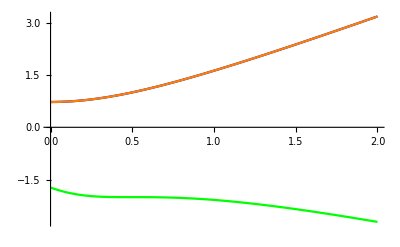

```mathematica
P
Q
PQ=Numerator[Factor[P-Q]];
Collect[Factor[PQ],λ]
y1sol=Solve[S==0,Subscript[y, 1]]
PQfac=Factor[PQ/.y1sol][[1]]
xxi={Subscript[x, 1]->Subscript[A, 1]+Subscript[ξ, 1],Subscript[x, 2]->Subscript[A, 2]+Subscript[ξ, 2]}
Factor[diff/.y1sol/.xxi/.{λ->1}]
factorlist=FactorList[PQfac];
remaining=factorlist[[4]][[1]]/.xxi
lambdaremaining=Solve[(remaining/.xxi)==0,λ]
lambdaremaining = λ/.lambdaremaining
Factor[Numerator[lambdaremaining]-Denominator[lambdaremaining]]
```

c_1/(-A_1+x_1)+(c_2 (B_1+x_1))/((-A_1+x_1) (-A_2+x_2))

c_1/(-A_1+λ y_1)+(c_2 (B_1+λ y_1))/((-A_2+λ x_2) (-A_1+λ y_1))

-A_2^2 c_1 x_1+A_1 A_2 c_2 x_1+A_2 B_1 c_2 x_1+A_1 B_1 c_2 x_2+A_2 c_1 x_1 x_2-B_1 c_2 x_1 x_2+λ (-A_1 B_1 c_2 x_2+A_2 c_1 x_1 x_2-A_1 c_2 x_1 x_2-c_1 x_1 x_2^2+A_2^2 c_1 y_1-A_1 A_2 c_2 y_1-A_2 B_1 c_2 y_1-A_2 c_1 x_2 y_1+A_1 c_2 x_2 y_1-c_2 x_1 x_2 y_1)+λ^2 (-A_2 c_1 x_2 y_1+B_1 c_2 x_2 y_1+c_2 x_1 x_2 y_1+c_1 x_2^2 y_1)

{{y_1→(x_1+x_2-λ x_2)/λ}}

-(-1+λ) x_2 (A_2^2 c_1-A_1 A_2 c_2+A_1 B_1 c_2-A_2 B_1 c_2+A_1 c_2 x_1-B_1 c_2 x_1-c_2 x_1^2-A_2 c_1 x_2-λ A_2 c_1 x_2+A_1 c_2 x_2+λ B_1 c_2 x_2-c_2 x_1 x_2+λ c_2 x_1 x_2+λ c_1 x_2^2)

{x_1→A_1+ξ_1,x_2→A_2+ξ_2}

{-(-A_1 c_2 ξ_1-B_1 c_2 ξ_1-c_2 ξ_1^2+A_1 c_2 ξ_2+B_1 c_2 ξ_2+c_1 ξ_2^2)/(ξ_1^2 ξ_2^2)}

A_2^2 c_1-A_1 A_2 c_2+A_1 B_1 c_2-A_2 B_1 c_2+A_1 c_2 (A_1+ξ_1)-B_1 c_2 (A_1+ξ_1)-c_2 (A_1+ξ_1)^2-A_2 c_1 (A_2+ξ_2)-λ A_2 c_1 (A_2+ξ_2)+A_1 c_2 (A_2+ξ_2)+λ B_1 c_2 (A_2+ξ_2)-c_2 (A_1+ξ_1) (A_2+ξ_2)+λ c_2 (A_1+ξ_1) (A_2+ξ_2)+λ c_1 (A_2+ξ_2)^2

{{λ→(A_1 A_2 c_2+A_2 B_1 c_2+A_1 c_2 ξ_1+A_2 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2+A_2 c_1 ξ_2+c_2 ξ_1 ξ_2)/((A_2+ξ_2) (A_1 c_2+B_1 c_2+c_2 ξ_1+c_1 ξ_2))}}

{(A_1 A_2 c_2+A_2 B_1 c_2+A_1 c_2 ξ_1+A_2 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2+A_2 c_1 ξ_2+c_2 ξ_1 ξ_2)/((A_2+ξ_2) (A_1 c_2+B_1 c_2+c_2 ξ_1+c_1 ξ_2))}

{A_1 c_2 ξ_1+B_1 c_2 ξ_1+c_2 ξ_1^2-A_1 c_2 ξ_2-B_1 c_2 ξ_2-c_1 ξ_2^2}